```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

## Functions that generate lists of integer "clues", and function to ID sessie network

### Explanations

MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

Note: these first three provide lists of numbers based sessie events / network nodes, so as soon as a "Verdict" has been assigned, the CheckDimensions summaries can be used by GuessDimension and TestForUnusedRules.

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

#### CheckDimensions: accepts a list of "significant" positive integers, returns {"1D"|"2D"|...|"exp", n, {k, delay, matchlen, match}, dt}, indicating an n-dimensional or exponential network. Pattern detection required k-averaging, and a delay before the pattern was established and a difference or ratio match of length matchlen was detected. The difference table dt is provided for human inspection, but in theory it (but not the network) could be summarized as {n, dt⟦All, delay;;delay+k⟧} or {"exp", dt⟦All, delay;;delay+k⟧}, respectively. (In fact, only the first element of each row is needed, until the final row.) It is not currently clear whether k and match have any useful meaning in the exponential summary, but both can be reconstructed from the difference table summary. The function GuessDimension collects IDs ("1D", "2D", etc.) returned for any of the 4 significant number generator functions, and considers matchlen as a measure of reliability.

#### GuessDimension: with appropriate checks, tries all 4 approximative tests by applying CheckDimensions to the lists described above. Sessie is auto-extended to try to reach agreement. Changes "Verdict" if the combined matchlen values returned indicate satisfactory reliability.

#### TestForUnusedRules: decides whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

#### Possible issues & notes:

(1) If dt⟦1,1⟧ == j ≠ 1, there was some initial stuff before the pattern set in.

Solution: If the numbers were provided by either MaxStateLengthPositions or LeastUsedRulePositions, toss out the first j-1 steps of the sessie to generate a network with a difference table in which the first j-1 columns are dropped, and the first row entries are all reduced by subtracting j-1.  If the numbers were produced from the "Net", it's unclear how much of the sessie state strings should be skipped.

(2) Once reliable ID has been made, call TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible:  affects acceleration.  Later call ImproveInitialState (not yet written), to discard initial or final tagged cells unchanged by the evolution:  only affects sessie display, not the network.  Think carefully about unchanged interior tagged cells:  removing an inert cell might allow a different evolution.

(*) Once we have a network summary...:  Depending on the initial state string, a different network summary might be generated:  how to recognize their equivalence?

Possible solution: Make k alternative summaries, treating by dropping 0, 1, …, k-1 states [as in (1)], sort them (perhaps by last row, then next-to-last, etc.), treat as "canonical" the first in the sorted list.

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% -- ARBITRARY! -- of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals -- IS THIS NECESSARY?! -- and return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss]; (* update it if changed *)
Print[vdct];
ans
];
```

## Examples of ID function & clues usage

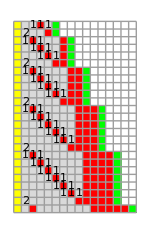


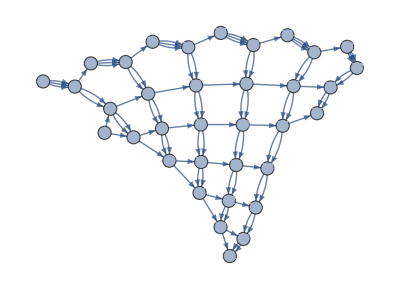
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss90=SSS[{"ABA"->"AAB","A"->"ABA"}, "CAABAD",75,SSSMax->25, NetMax->35,SSSSize->150,NetSize->400, VertexSize->0.6];
```

```mathematica
sss90["RuleSet"]
```

{ABA→AAB,A→ABA}

```mathematica
sss90["Evolution"]
```

{CAABAD,CAAABD,CABAAABD,CAABAABD,CAAABABD,CAAAABBD,CABAAAABBD,CAABAAABBD,CAAABAABBD,CAAAABABBD,CAAAAABBBD,CABAAAAABBBD,CAABAAAABBBD,CAAABAAABBBD,CAAAABAABBBD,CAAAAABABBBD,CAAAAAABBBBD,CABAAAAAABBBBD,CAABAAAAABBBBD,CAAABAAAABBBBD,CAAAABAAABBBBD,CAAAAABAABBBBD,CAAAAAABABBBBD,CAAAAAAABBBBBD,CABAAAAAAABBBBBD,CAABAAAAAABBBBBD,CAAABAAAAABBBBBD,CAAAABAAAABBBBBD,CAAAAABAAABBBBBD,CAAAAAABAABBBBBD,CAAAAAAABABBBBBD,CAAAAAAAABBBBBBD,CABAAAAAAAABBBBBBD,CAABAAAAAAABBBBBBD,CAAABAAAAAABBBBBBD,CAAAABAAAAABBBBBBD,CAAAAABAAAABBBBBBD,CAAAAAABAAABBBBBBD,CAAAAAAABAABBBBBBD,CAAAAAAAABABBBBBBD,CAAAAAAAAABBBBBBBD,CABAAAAAAAAABBBBBBBD,CAABAAAAAAAABBBBBBBD,CAAABAAAAAAABBBBBBBD,CAAAABAAAAAABBBBBBBD,CAAAAABAAAAABBBBBBBD,CAAAAAABAAAABBBBBBBD,CAAAAAAABAAABBBBBBBD,CAAAAAAAABAABBBBBBBD,CAAAAAAAAABABBBBBBBD,CAAAAAAAAAABBBBBBBBD,CABAAAAAAAAAABBBBBBBBD,CAABAAAAAAAAABBBBBBBBD,CAAABAAAAAAAABBBBBBBBD,CAAAABAAAAAAABBBBBBBBD,CAAAAABAAAAAABBBBBBBBD,CAAAAAABAAAAABBBBBBBBD,CAAAAAAABAAAABBBBBBBBD,CAAAAAAAABAAABBBBBBBBD,CAAAAAAAAABAABBBBBBBBD,CAAAAAAAAAABABBBBBBBBD,CAAAAAAAAAAABBBBBBBBBD,CABAAAAAAAAAAABBBBBBBBBD,CAABAAAAAAAAAABBBBBBBBBD,CAAABAAAAAAAAABBBBBBBBBD,CAAAABAAAAAAAABBBBBBBBBD,CAAAAABAAAAAAABBBBBBBBBD,CAAAAAABAAAAAABBBBBBBBBD,CAAAAAAABAAAAABBBBBBBBBD,CAAAAAAAABAAAABBBBBBBBBD,CAAAAAAAAABAAABBBBBBBBBD,CAAAAAAAAAABAABBBBBBBBBD,CAAAAAAAAAAABABBBBBBBBBD,CAAAAAAAAAAAABBBBBBBBBBD,CABAAAAAAAAAAAABBBBBBBBBBD,CAABAAAAAAAAAAABBBBBBBBBBD}

```mathematica
sss90["Net"]
```

{2→3,2→3,2→3,3→4,3→4,1→4,4→5,4→5,1→5,3→6,6→7,6→7,6→7,7→8,7→8,4→8,8→9,8→9,5→9,9→10,9→10,5→10,7→11,11→12,11→12,11→12,12→13,12→13,8→13,13→14,13→14,9→14,14→15,14→15,10→15,15→16,15→16,10→16,12→17,17→18,17→18,17→18,18→19,18→19,13→19,19→20,19→20,14→20,20→21,20→21,15→21,21→22,21→22,16→22,22→23,22→23,16→23,18→24,24→25,24→25,24→25,25→26,25→26,19→26,26→27,26→27,20→27,27→28,27→28,21→28,28→29,28→29,22→29,29→30,29→30,23→30,30→31,30→31,23→31,25→32,32→33,32→33,32→33,33→34,33→34,26→34,34→35,34→35,27→35,35→36,35→36,28→36,36→37,36→37,29→37,37→38,37→38,30→38,38→39,38→39,31→39,39→40,39→40,31→40,33→41,41→42,41→42,41→42,42→43,42→43,34→43,43→44,43→44,35→44,44→45,44→45,36→45,45→46,45→46,37→46,46→47,46→47,38→47,47→48,47→48,39→48,48→49,48→49,40→49,49→50,49→50,40→50,42→51,51→52,51→52,51→52,52→53,52→53,43→53,53→54,53→54,44→54,54→55,54→55,45→55,55→56,55→56,46→56,56→57,56→57,47→57,57→58,57→58,48→58,58→59,58→59,49→59,59→60,59→60,50→60,60→61,60→61,50→61,52→62,62→63,62→63,62→63,63→64,63→64,53→64,64→65,64→65,54→65,65→66,65→66,55→66,66→67,66→67,56→67,67→68,67→68,57→68,68→69,68→69,58→69,69→70,69→70,59→70,70→71,70→71,60→71,71→72,71→72,61→72,72→73,72→73,61→73,63→74,74→75,74→75,74→75}

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

```mathematica
MaxStateLengthPositions[sss90]
```

{3,7,12,18,25,33,42,52,63}

Visually, these are the positions in the sessie (colored) image where the state string got longer.

```mathematica
CheckDimension@MaxStateLengthPositions[sss90]
```

{2D,{1,0,7,1},3
4
1,3 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

Identified as (probably) 2-dimensional, pattern valid starting from position 3.  In the 0^th row, provided by MaxStateLengthPositions, we see rapid, increasing growth.  In the row of 1^st differences, growth is linear.  The 2^nd differences row is constant, and the 3^rd differences row would be all 0.  (This is reminiscent of taking derivatives of a quadratic (2^nd-degree) polynomial:  the first derivative is a linear function, the 2^nd is a constant, the 3^rd is zero.

In this case it would make sense to rerun SSS, starting with row 3, since apparently the pattern did not stabilize until then:

```mathematica
sss90["Evolution"]⟦3⟧
```

CABAAABD

Other points to discuss:

Is dropping the first 10% a good strategy?  Is there a better one?

Is demanding 5 reps a good strategy?  What if after 5 reps, the pattern changes?  (Unlikely, for this MaxStateLengthPositions.)

Is demanding that the same rules must be used in all meaningful intervals a good strategy?  (MergeIntervalsByRulesUsed)

#### LeastUsedRulePositions: positions where the least-used rule was used

```mathematica
LeastUsedRulePositions[sss90]
```

{2,6,11,17,24,32,41,51,62,74}

```mathematica
sss90["RulesUsed"]
```

{1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1}

```mathematica
CheckDimension@LeastUsedRulePositions[sss90]
```

{2D,{1,0,8,1},2
4
1,2 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

Again, the 2nd differences row is constant, indicating 2-d behavior.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last node that is n steps from origin on the undirected graph of "Net".

```mathematica
CheckDimension@DistanceLastPositions[sss90]
```

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,1,1,1,1,1,1,3,0,3}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,1,1,1,1,1,1,1,3,0,3}}

Position of first untrustworthy node: {61,64,65,66,67,68,69,70,71,72,73,75}

distances (uncut): {3,2,1,0,1,3,3,2,2,2,4,4,3,3,3,3,5,5,4,4,4,4,4,6,6,5,5,5,5,5,5,7,7,6,6,6,6,6,6,6,8,8,7,7,7,7,7,7,7,7,9,9,8,8,8,8,8,8,8,8,8,10,10,9,9,9,9,9,9,9,9,9,9,11,12}

last distance we'll trust: 8

{2D,{1,0,6,1},5
5
1,5 | 10 | 16 | 23 | 31 | 40 | 50 | 61
5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 |  | }

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization for the directed graph.)

```mathematica
CheckDimension@DistanceTally[sss90]
```

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,1,1,1,1,1,1,3,0,3}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,1,1,1,1,1,1,1,3,0,3}}

Position of first untrustworthy node: {61,64,65,66,67,68,69,70,71,72,73,75}

distances (uncut): {3,2,1,0,1,3,3,2,2,2,4,4,3,3,3,3,5,5,4,4,4,4,4,6,6,5,5,5,5,5,5,7,7,6,6,6,6,6,6,6,8,8,7,7,7,7,7,7,7,7,9,9,8,8,8,8,8,8,8,8,8,10,10,9,9,9,9,9,9,9,9,9,9,11,12}

last distance we'll trust: 8

{failed,1 | 3 | 7 | 14 | 21 | 29 | 38 | 48 | 59
2 | 4 | 7 | 7 | 8 | 9 | 10 | 11 | 
2 | 3 | 0 | 1 | 1 | 1 | 1 |  | 
1 | -3 | 1 | 0 | 0 | 0 |  |  | 
-4 | 4 | -1 | 0 | 0 |  |  |  | 
8 | -5 | 1 | 0 |  |  |  |  | }

```mathematica
SSSAnimate[sss90,VertexLabels->"VertexWeight",NetSize->400]
```

#### GuessDimension: tries all 4 approximative tests, with appropriate checks, changes "Verdict" if appropriate.

```mathematica
GuessDimension[sss90]
```

evol len: 75

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,1,1,1,1,1,1,3,0,3}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,1,1,1,1,1,1,1,3,0,3}}

Position of first untrustworthy node: {61,64,65,66,67,68,69,70,71,72,73,75}

distances (uncut): {3,2,1,0,1,3,3,2,2,2,4,4,3,3,3,3,5,5,4,4,4,4,4,6,6,5,5,5,5,5,5,7,7,6,6,6,6,6,6,6,8,8,7,7,7,7,7,7,7,7,9,9,8,8,8,8,8,8,8,8,8,10,10,9,9,9,9,9,9,9,9,9,9,11,12}

last distance we'll trust: 8

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,1,1,1,1,1,1,3,0,3}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,1,1,1,1,1,1,1,3,0,3}}

Position of first untrustworthy node: {61,64,65,66,67,68,69,70,71,72,73,75}

distances (uncut): {3,2,1,0,1,3,3,2,2,2,4,4,3,3,3,3,5,5,4,4,4,4,4,6,6,5,5,5,5,5,5,7,7,6,6,6,6,6,6,6,8,8,7,7,7,7,7,7,7,7,9,9,8,8,8,8,8,8,8,8,8,10,10,9,9,9,9,9,9,9,9,9,9,11,12}

last distance we'll trust: 8

{{2D,21}}

2D

{{2D,{1,0,7,1},3
4
1,3 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,8,1},2
4
1,2 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,6,1},5
5
1,5 | 10 | 16 | 23 | 31 | 40 | 50 | 61
5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 |  | }}

```mathematica
sss90["Verdict"]
```

2D

#### Other examples:

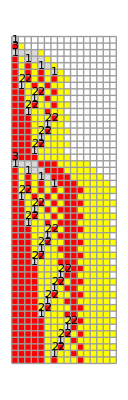
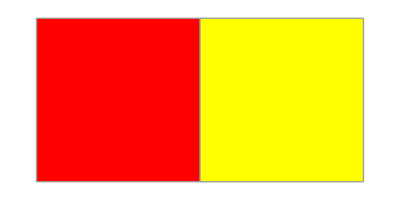
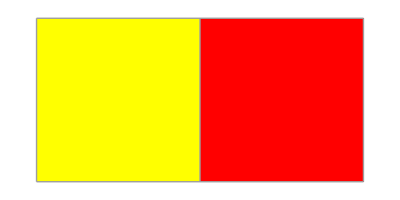

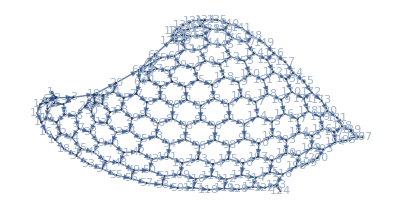
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssTemp=SSS[{"A"->"BC","CB"->"A","B"->"AAAA"},"A",700,SSSMax->50,NetMax->200];
```

```mathematica
sssTemp["RulesUsed"]
```

{1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2}

```mathematica
CheckDimension[LeastUsedRulePositions[sssTemp]]
```

{2D,{1,0,6,24},2
17
24,2 | 19 | 60 | 125 | 214 | 327 | 464 | 625
17 | 41 | 65 | 89 | 113 | 137 | 161 | 
24 | 24 | 24 | 24 | 24 | 24 |  | }

```mathematica
CheckDimension[MaxStateLengthPositions[sssTemp]]
```

{2D,{1,0,5,24},7
17
24,7 | 24 | 65 | 130 | 219 | 332 | 469
17 | 41 | 65 | 89 | 113 | 137 | 
24 | 24 | 24 | 24 | 24 |  | }

```mathematica
CheckDimension[DistanceLastPositions[sssTemp]]
```

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,2,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,2,0,1,1}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,2,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,2,0,1,1}}

Position of first untrustworthy node: {457,459,461,463,528,536,544,552,560,568,576,584,592,600,608,616,618,620,622,624,626,631,635,641,649,657,665,673,681,689,695,697,699,700}

distances (uncut): {0,1,2,2,2,2,3,4,3,4,5,6,3,4,5,6,7,8,3,4,4,4,4,5,6,5,6,7,8,5,6,7,8,9,10,5,6,7,8,9,10,11,12,7,8,9,10,11,12,13,14,9,10,11,12,13,14,15,16,5,6,6,6,6,7,8,7,8,9,10,7,8,9,10,11,12,7,8,9,10,11,12,13,14,9,10,11,12,13,14,15,16,11,12,13,14,15,16,17,18,13,14,15,16,17,18,19,20,15,16,17,18,19,20,21,22,17,18,19,20,21,22,23,24,7,8,8,8,8,9,10,9,10,11,12,9,10,11,12,13,14,9,10,11,12,13,14,15,16,11,12,13,14,15,16,17,18,13,14,15,16,17,18,19,20,15,16,17,18,19,20,21,22,17,18,19,20,21,22,23,24,19,20,21,22,23,24,25,26,21,22,23,24,25,26,27,28,23,24,25,26,27,28,29,30,25,26,27,28,29,30,31,32,9,10,10,10,10,11,12,11,12,13,14,11,12,13,14,15,16,11,12,13,14,15,16,17,18,13,14,15,16,17,18,19,20,15,16,17,18,19,20,21,22,17,18,19,20,21,22,23,24,19,20,21,22,23,24,25,26,21,22,23,24,25,26,27,28,23,24,25,26,27,28,29,30,25,26,27,28,29,30,31,32,27,28,29,30,31,32,33,34,29,30,31,32,33,34,35,36,31,32,33,34,35,36,37,38,33,34,35,36,37,38,39,40,11,12,12,12,12,13,14,13,14,15,16,13,14,15,16,17,18,13,14,15,16,17,18,19,20,15,16,17,18,19,20,21,22,17,18,19,20,21,22,23,24,19,20,21,22,23,24,25,26,21,22,23,24,25,26,27,28,23,24,25,26,27,28,29,30,25,26,27,28,29,30,31,32,27,28,29,30,31,32,33,34,29,30,31,32,33,34,35,36,31,32,33,34,35,36,37,38,33,34,35,36,37,38,39,40,35,36,37,38,39,40,41,42,37,38,39,40,41,42,43,44,39,40,41,42,43,44,45,46,41,42,43,44,45,46,47,48,13,14,14,14,14,15,16,15,16,17,18,15,16,17,18,19,20,15,16,17,18,19,20,21,22,17,18,19,20,21,22,23,24,19,20,21,22,23,24,25,26,21,22,23,24,25,26,27,28,23,24,25,26,27,28,29,30,25,26,27,28,29,30,31,32,27,28,29,30,31,32,33,34,29,30,31,32,33,34,35,36,31,32,33,34,35,36,37,38,33,34,35,36,37,38,39,40,35,36,37,38,39,40,41,42,37,38,39,40,41,42,43,44,39,40,41,42,43,44,45,46,41,42,43,44,45,46,47,48,43,44,45,46,47,48,49,50,45,46,47,48,49,50,51,52,47,48,49,50,51,52,53,54,49,50,51,52,53,54,55,56,15,16,16,16,16,17,18,17,18,19,20,17,18,19,20,21,22,17,18,19,20,21,22,23,24,19,20,21,22,23,24,25,26,21,22,23,24,25,26,27,28,23,24,25,26,27,28,29,30,25,26,27,28,29,30,31,32,27,28,29,30,31,32,33,34,29,30,31,32,33,34,35,36,31,32,33}

last distance we'll trust: 16

{2D,{1,0,6,24},6
17
24,6 | 23 | 64 | 129 | 218 | 331 | 468 | 629
17 | 41 | 65 | 89 | 113 | 137 | 161 | 
24 | 24 | 24 | 24 | 24 | 24 |  | }

```mathematica
CheckDimension[DistanceTally[sssTemp]]
```

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,2,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,2,0,1,1}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,2,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,2,0,1,1}}

Position of first untrustworthy node: {457,459,461,463,528,536,544,552,560,568,576,584,592,600,608,616,618,620,622,624,626,631,635,641,649,657,665,673,681,689,695,697,699,700}

distances (uncut): {0,1,2,2,2,2,3,4,3,4,5,6,3,4,5,6,7,8,3,4,4,4,4,5,6,5,6,7,8,5,6,7,8,9,10,5,6,7,8,9,10,11,12,7,8,9,10,11,12,13,14,9,10,11,12,13,14,15,16,5,6,6,6,6,7,8,7,8,9,10,7,8,9,10,11,12,7,8,9,10,11,12,13,14,9,10,11,12,13,14,15,16,11,12,13,14,15,16,17,18,13,14,15,16,17,18,19,20,15,16,17,18,19,20,21,22,17,18,19,20,21,22,23,24,7,8,8,8,8,9,10,9,10,11,12,9,10,11,12,13,14,9,10,11,12,13,14,15,16,11,12,13,14,15,16,17,18,13,14,15,16,17,18,19,20,15,16,17,18,19,20,21,22,17,18,19,20,21,22,23,24,19,20,21,22,23,24,25,26,21,22,23,24,25,26,27,28,23,24,25,26,27,28,29,30,25,26,27,28,29,30,31,32,9,10,10,10,10,11,12,11,12,13,14,11,12,13,14,15,16,11,12,13,14,15,16,17,18,13,14,15,16,17,18,19,20,15,16,17,18,19,20,21,22,17,18,19,20,21,22,23,24,19,20,21,22,23,24,25,26,21,22,23,24,25,26,27,28,23,24,25,26,27,28,29,30,25,26,27,28,29,30,31,32,27,28,29,30,31,32,33,34,29,30,31,32,33,34,35,36,31,32,33,34,35,36,37,38,33,34,35,36,37,38,39,40,11,12,12,12,12,13,14,13,14,15,16,13,14,15,16,17,18,13,14,15,16,17,18,19,20,15,16,17,18,19,20,21,22,17,18,19,20,21,22,23,24,19,20,21,22,23,24,25,26,21,22,23,24,25,26,27,28,23,24,25,26,27,28,29,30,25,26,27,28,29,30,31,32,27,28,29,30,31,32,33,34,29,30,31,32,33,34,35,36,31,32,33,34,35,36,37,38,33,34,35,36,37,38,39,40,35,36,37,38,39,40,41,42,37,38,39,40,41,42,43,44,39,40,41,42,43,44,45,46,41,42,43,44,45,46,47,48,13,14,14,14,14,15,16,15,16,17,18,15,16,17,18,19,20,15,16,17,18,19,20,21,22,17,18,19,20,21,22,23,24,19,20,21,22,23,24,25,26,21,22,23,24,25,26,27,28,23,24,25,26,27,28,29,30,25,26,27,28,29,30,31,32,27,28,29,30,31,32,33,34,29,30,31,32,33,34,35,36,31,32,33,34,35,36,37,38,33,34,35,36,37,38,39,40,35,36,37,38,39,40,41,42,37,38,39,40,41,42,43,44,39,40,41,42,43,44,45,46,41,42,43,44,45,46,47,48,43,44,45,46,47,48,49,50,45,46,47,48,49,50,51,52,47,48,49,50,51,52,53,54,49,50,51,52,53,54,55,56,15,16,16,16,16,17,18,17,18,19,20,17,18,19,20,21,22,17,18,19,20,21,22,23,24,19,20,21,22,23,24,25,26,21,22,23,24,25,26,27,28,23,24,25,26,27,28,29,30,25,26,27,28,29,30,31,32,27,28,29,30,31,32,33,34,29,30,31,32,33,34,35,36,31,32,33}

last distance we'll trust: 16

{2D,{2,0,14,3/2},1 | 2
1 | 4
3 | 0,1 | 2 | 6 | 10 | 17 | 24 | 34 | 44 | 57 | 70 | 86 | 102 | 121 | 140 | 162 | 184 | 209
1 | 4 | 4 | 7 | 7 | 10 | 10 | 13 | 13 | 16 | 16 | 19 | 19 | 22 | 22 | 25 | 
3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 |  | }

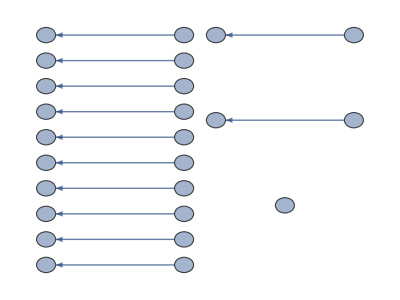
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Repeating

```mathematica
sss1a=SSS[{"A"->"",""->"A"},"",25,SSSSize->{50,200},NetSize->{400,300}, VertexSize->0.6];
sss1a["Verdict"]
```

```mathematica
CheckDimension@LeastUsedRulePositions[sss1a]
```

{1D,{1,0,11,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@MaxStateLengthPositions[sss1a]
```

{1D,{1,0,11,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@DistanceLastPositions[sss1a]
```

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1}}

Position of first untrustworthy node: {25}

distances (uncut): {0,1,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

Part::partw: Part {25} of {0,1,∞,∞,∞,∞,∞,∞,∞,∞,«14»} does not exist.

last distance we'll trust: {0,1,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}⟦{25}⟧

{failed,2
}

```mathematica
CheckDimension@DistanceTally[sss1a]
```

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1}}

Position of first untrustworthy node: {25}

distances (uncut): {0,1,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

Part::partw: Part {25} of {0,1,∞,∞,∞,∞,∞,∞,∞,∞,«14»} does not exist.

last distance we'll trust: {0,1,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}⟦{25}⟧

{failed,1
}

```mathematica
GuessDimension[sss1a]
```

Repeating

If the sessie is disconnected, neither DistanceTally nor DistanceLastPositions may generate a usable list.  But fortunately, any repeating sessie can automatically be assumed to have dimension 1.   This is supported by all tests for repeating, connected cases.  So GuessDimension returns immediately in these cases.

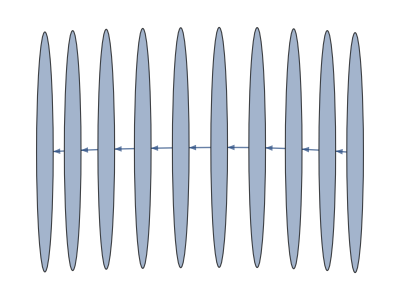
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

Repeating

Repeating

TestForUnusedRules[<|Net→{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20},OutDegreePotential→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},OutDegreeRemaining→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},OutDegreeActual→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},InDegree→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},ConnectionList→{{1}→{2},{2}→{3},{3}→{4},{4}→{5},{5}→{6},{6}→{7},{7}→{8},{8}→{9},{9}→{10},{10}→{11},{11}→{12},{12}→{13},{13}→{14},{14}→{15},{15}→{16},{16}→{17},{17}→{18},{18}→{19},{19}→{20},{20}→{21}},Verdict→Repeating,RulesUsed→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},CellsDeleted→{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}},Distance→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},MaxColor→6,TagIndex→22,TEvolution→{s[{0,1}],s[{0,2}],s[{0,3}],s[{0,4}],s[{0,5}],s[{0,6}],s[{0,7}],s[{0,8}],s[{0,9}],s[{0,10}],s[{0,11}],s[{0,12}],s[{0,13}],s[{0,14}],s[{0,15}],s[{0,16}],s[{0,17}],s[{0,18}],s[{0,19}],s[{0,20}],s[{0,21}]},Evolution→{A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A},RuleSet→{A→A},TRuleSet→{s[{0,lhsTag$27169_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$27169}→$SSSTagIndex+{0}];s[{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]},RuleSetWeight→2,RuleSetLength→2|>]

```mathematica
sss1b=SSS[4,20,SSSSize->{50,200},Max->10,NetSize->{400,300}, VertexSize->0.6];
sss1b["Verdict"]
GuessDimension[sss1b]
TestForUnusedRules[sss1b]
```

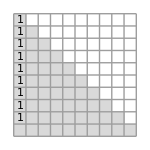
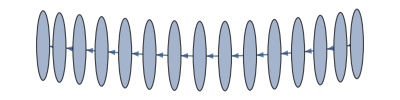
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

OK

evol len: 20

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2}

treating as zero (in odr): 1

using "OutDegreeRemaining" to find end of reliable data: {{∞},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2}}

Position of first untrustworthy node: {20}

distances (uncut): {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

last distance we'll trust: 19

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2}

treating as zero (in odr): 1

using "OutDegreeRemaining" to find end of reliable data: {{∞},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2}}

Position of first untrustworthy node: {20}

distances (uncut): {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

last distance we'll trust: 19

{{1D,73}}

1D

{1D,{1,0,18,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{1D,{1,0,19,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{1D,{1,0,18,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{1D,{1,0,18,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

1D

TestForUnusedRules[<|Net→{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20},OutDegreePotential→{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},OutDegreeRemaining→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2},OutDegreeActual→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},InDegree→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},ConnectionList→{{1}→{2,3},{2}→{4,5},{4}→{6,7},{6}→{8,9},{8}→{10,11},{10}→{12,13},{12}→{14,15},{14}→{16,17},{16}→{18,19},{18}→{20,21},{20}→{22,23},{22}→{24,25},{24}→{26,27},{26}→{28,29},{28}→{30,31},{30}→{32,33},{32}→{34,35},{34}→{36,37},{36}→{38,39},{38}→{40,41}},Verdict→1D,RulesUsed→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},CellsDeleted→{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}},Distance→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},MaxColor→6,TagIndex→42,TEvolution→{s[{0,1}],s[{0,2},{0,3}],s[{0,4},{0,5},{0,3}],s[{0,6},{0,7},{0,5},{0,3}],s[{0,8},{0,9},{0,7},{0,5},{0,3}],s[{0,10},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,12},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,14},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,16},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,18},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,20},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,22},{0,23},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,24},{0,25},{0,23},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,26},{0,27},{0,25},{0,23},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,28},{0,29},{0,27},{0,25},{0,23},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,30},{0,31},{0,29},{0,27},{0,25},{0,23},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,32},{0,33},{0,31},{0,29},{0,27},{0,25},{0,23},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,34},{0,35},{0,33},{0,31},{0,29},{0,27},{0,25},{0,23},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,36},{0,37},{0,35},{0,33},{0,31},{0,29},{0,27},{0,25},{0,23},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,38},{0,39},{0,37},{0,35},{0,33},{0,31},{0,29},{0,27},{0,25},{0,23},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}],s[{0,40},{0,41},{0,39},{0,37},{0,35},{0,33},{0,31},{0,29},{0,27},{0,25},{0,23},{0,21},{0,19},{0,17},{0,15},{0,13},{0,11},{0,9},{0,7},{0,5},{0,3}]},Evolution→{A,AA,AAA,AAAA,AAAAA,AAAAAA,AAAAAAA,AAAAAAAA,AAAAAAAAA,AAAAAAAAAA,AAAAAAAAAAA,AAAAAAAAAAAA,AAAAAAAAAAAAA,AAAAAAAAAAAAAA,AAAAAAAAAAAAAAA,AAAAAAAAAAAAAAAA,AAAAAAAAAAAAAAAAA,AAAAAAAAAAAAAAAAAA,AAAAAAAAAAAAAAAAAAA,AAAAAAAAAAAAAAAAAAAA,AAAAAAAAAAAAAAAAAAAAA},RuleSet→{A→AA},TRuleSet→{s[{0,lhsTag$27337_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$27337}→$SSSTagIndex+{0,1}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]},RuleSetWeight→3,RuleSetLength→3|>]

```mathematica
sss20=SSS[20,20,SSSMax->10,SSSSize->{150,150},NetMax->15,NetSize->{400,100}, VertexSize->.8];
sss20["Verdict"]
GuessDimension[sss20]//Column
sss20["Verdict"]
TestForUnusedRules[sss20]
```

Note that GuessDimension has changed the "Verdict" field of sss20.

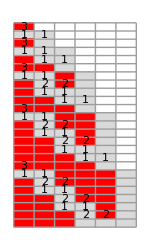


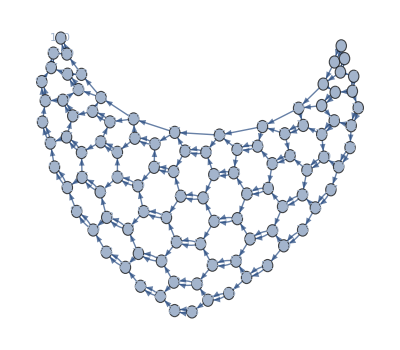
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

OK

evol len: 100

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,∞,∞},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2}}

Position of first untrustworthy node: {82,84,86,88,90,92,94,96,98,100}

distances (uncut): {0,1,2,3,2,4,4,3,4,3,5,6,5,5,4,5,4,7,7,6,7,6,6,5,6,5,8,9,8,8,7,8,7,7,6,7,6,10,10,9,10,9,9,8,9,8,8,7,8,7,11,12,11,11,10,11,10,10,9,10,9,9,8,9,8,13,13,12,13,12,12,11,12,11,11,10,11,10,10,9,10,9,14,15,14,14,13,14,13,13,12,13,12,12,11,12,11,11,10,11}

last distance we'll trust: 9

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,∞,∞},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2}}

Position of first untrustworthy node: {82,84,86,88,90,92,94,96,98,100}

distances (uncut): {0,1,2,3,2,4,4,3,4,3,5,6,5,5,4,5,4,7,7,6,7,6,6,5,6,5,8,9,8,8,7,8,7,7,6,7,6,10,10,9,10,9,9,8,9,8,8,7,8,7,11,12,11,11,10,11,10,10,9,10,9,9,8,9,8,13,13,12,13,12,12,11,12,11,11,10,11,10,10,9,10,9,14,15,14,14,13,14,13,13,12,13,12,12,11,12,11,11,10,11}

last distance we'll trust: 9

{{2D,23}}

2D

{2D,{1,0,5,2},7
5
2,7 | 12 | 19 | 28 | 39 | 52 | 67
5 | 7 | 9 | 11 | 13 | 15 | 
2 | 2 | 2 | 2 | 2 |  | }
{2D,{1,0,6,2},6
5
2,6 | 11 | 18 | 27 | 38 | 51 | 66 | 83
5 | 7 | 9 | 11 | 13 | 15 | 17 | 
2 | 2 | 2 | 2 | 2 | 2 |  | }
{2D,{1,0,6,2},5
5
2,5 | 10 | 17 | 26 | 37 | 50 | 65 | 82
5 | 7 | 9 | 11 | 13 | 15 | 17 | 
2 | 2 | 2 | 2 | 2 | 2 |  | }
{2D,{3,0,6,4/3},1 | 2 | 4
1 | 2 | 3
1 | 1 | 2,1 | 2 | 4 | 7 | 12 | 18 | 25 | 34 | 44 | 55
1 | 2 | 3 | 5 | 6 | 7 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 |  | }

2D

```mathematica
sssHex=SSS[{"AA"->"BA","AB"->"AA","B"->"AA"},"B",100,SSSMax->25,SSSSize->{150,250},NetMax->100,NetSize->{400,350}, VertexSize->1];
sssHex["Verdict"]
GuessDimension[sssHex]//Column
sssHex["Verdict"]
```

```mathematica
TestForUnusedRules[sssHex]
```

TestForUnusedRules[<|Net→{1→2,1→2,2→3,3→4,3→4,4→5,2→5,4→6,6→7,6→7,7→8,5→8,8→9,8→9,9→10,5→10,7→11,11→12,11→12,12→13,9→13,13→14,13→14,14→15,10→15,15→16,15→16,16→17,10→17,12→18,18→19,18→19,19→20,14→20,20→21,20→21,21→22,16→22,22→23,22→23,23→24,17→24,24→25,24→25,25→26,17→26,19→27,27→28,27→28,28→29,21→29,29→30,29→30,30→31,23→31,31→32,31→32,32→33,25→33,33→34,33→34,34→35,26→35,35→36,35→36,36→37,26→37,28→38,38→39,38→39,39→40,30→40,40→41,40→41,41→42,32→42,42→43,42→43,43→44,34→44,44→45,44→45,45→46,36→46,46→47,46→47,47→48,37→48,48→49,48→49,49→50,37→50,39→51,51→52,51→52,52→53,41→53,53→54,53→54,54→55,43→55,55→56,55→56,56→57,45→57,57→58,57→58,58→59,47→59,59→60,59→60,60→61,49→61,61→62,61→62,62→63,50→63,63→64,63→64,64→65,50→65,52→66,66→67,66→67,67→68,54→68,68→69,68→69,69→70,56→70,70→71,70→71,71→72,58→72,72→73,72→73,73→74,60→74,74→75,74→75,75→76,62→76,76→77,76→77,77→78,64→78,78→79,78→79,79→80,65→80,80→81,80→81,81→82,65→82,67→83,83→84,83→84,84→85,69→85,85→86,85→86,86→87,71→87,87→88,87→88,88→89,73→89,89→90,89→90,90→91,75→91,91→92,91→92,92→93,77→93,93→94,93→94,94→95,79→95,95→96,95→96,96→97,81→97,97→98,97→98,98→99,82→99,99→100,99→100},OutDegreePotential→{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},OutDegreeRemaining→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2},OutDegreeActual→{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,0},InDegree→{1,2,1,2,2,1,2,2,2,2,1,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},ConnectionList→{{1}→{2,3},{2,3}→{4,5},{4}→{6,7},{6,7}→{8,9},{9,5}→{10,11},{8}→{12,13},{12,13}→{14,15},{15,10}→{16,17},{16,17}→{18,19},{19,11}→{20,21},{14}→{22,23},{22,23}→{24,25},{25,18}→{26,27},{26,27}→{28,29},{29,20}→{30,31},{30,31}→{32,33},{33,21}→{34,35},{24}→{36,37},{36,37}→{38,39},{39,28}→{40,41},{40,41}→{42,43},{43,32}→{44,45},{44,45}→{46,47},{47,34}→{48,49},{48,49}→{50,51},{51,35}→{52,53},{38}→{54,55},{54,55}→{56,57},{57,42}→{58,59},{58,59}→{60,61},{61,46}→{62,63},{62,63}→{64,65},{65,50}→{66,67},{66,67}→{68,69},{69,52}→{70,71},{70,71}→{72,73},{73,53}→{74,75},{56}→{76,77},{76,77}→{78,79},{79,60}→{80,81},{80,81}→{82,83},{83,64}→{84,85},{84,85}→{86,87},{87,68}→{88,89},{88,89}→{90,91},{91,72}→{92,93},{92,93}→{94,95},{95,74}→{96,97},{96,97}→{98,99},{99,75}→{100,101},{78}→{102,103},{102,103}→{104,105},{105,82}→{106,107},{106,107}→{108,109},{109,86}→{110,111},{110,111}→{112,113},{113,90}→{114,115},{114,115}→{116,117},{117,94}→{118,119},{118,119}→{120,121},{121,98}→{122,123},{122,123}→{124,125},{125,100}→{126,127},{126,127}→{128,129},{129,101}→{130,131},{104}→{132,133},{132,133}→{134,135},{135,108}→{136,137},{136,137}→{138,139},{139,112}→{140,141},{140,141}→{142,143},{143,116}→{144,145},{144,145}→{146,147},{147,120}→{148,149},{148,149}→{150,151},{151,124}→{152,153},{152,153}→{154,155},{155,128}→{156,157},{156,157}→{158,159},{159,130}→{160,161},{160,161}→{162,163},{163,131}→{164,165},{134}→{166,167},{166,167}→{168,169},{169,138}→{170,171},{170,171}→{172,173},{173,142}→{174,175},{174,175}→{176,177},{177,146}→{178,179},{178,179}→{180,181},{181,150}→{182,183},{182,183}→{184,185},{185,154}→{186,187},{186,187}→{188,189},{189,158}→{190,191},{190,191}→{192,193},{193,162}→{194,195},{194,195}→{196,197},{197,164}→{198,199},{198,199}→{200,201}},Verdict→2D,RulesUsed→{3,1,3,1,1,3,1,2,1,1,3,1,2,1,2,1,1,3,1,2,1,2,1,2,1,1,3,1,2,1,2,1,2,1,2,1,1,3,1,2,1,2,1,2,1,2,1,2,1,1,3,1,2,1,2,1,2,1,2,1,2,1,2,1,1,3,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,1,3,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1},CellsDeleted→{{1},{1,2},{1},{1,2},{2,3},{1},{1,2},{2,3},{2,3},{3,4},{1},{1,2},{2,3},{2,3},{3,4},{3,4},{4,5},{1},{1,2},{2,3},{2,3},{3,4},{3,4},{4,5},{4,5},{5,6},{1},{1,2},{2,3},{2,3},{3,4},{3,4},{4,5},{4,5},{5,6},{5,6},{6,7},{1},{1,2},{2,3},{2,3},{3,4},{3,4},{4,5},{4,5},{5,6},{5,6},{6,7},{6,7},{7,8},{1},{1,2},{2,3},{2,3},{3,4},{3,4},{4,5},{4,5},{5,6},{5,6},{6,7},{6,7},{7,8},{7,8},{8,9},{1},{1,2},{2,3},{2,3},{3,4},{3,4},{4,5},{4,5},{5,6},{5,6},{6,7},{6,7},{7,8},{7,8},{8,9},{8,9},{9,10},{1},{1,2},{2,3},{2,3},{3,4},{3,4},{4,5},{4,5},{5,6},{5,6},{6,7},{6,7},{7,8},{7,8},{8,9},{8,9},{9,10},{9,10}},Distance→{0,1,2,3,2,4,5,3,4,3,6,7,5,6,4,5,4,8,9,7,8,6,7,5,6,5,10,11,9,10,8,9,7,8,6,7,6,12,13,11,12,10,11,9,10,8,9,7,8,7,14,15,13,14,12,13,11,12,10,11,9,10,8,9,8,16,17,15,16,14,15,13,14,12,13,11,12,10,11,9,10,9,18,19,17,18,16,17,15,16,14,15,13,14,12,13,11,12,10,11},MaxColor→6,TagIndex→202,TEvolution→{s[{1,1}],s[{0,2},{0,3}],s[{1,4},{0,5}],s[{0,6},{0,7},{0,5}],s[{1,8},{0,9},{0,5}],s[{1,8},{1,10},{0,11}],s[{0,12},{0,13},{1,10},{0,11}],s[{1,14},{0,15},{1,10},{0,11}],s[{1,14},{0,16},{0,17},{0,11}],s[{1,14},{1,18},{0,19},{0,11}],s[{1,14},{1,18},{1,20},{0,21}],s[{0,22},{0,23},{1,18},{1,20},{0,21}],s[{1,24},{0,25},{1,18},{1,20},{0,21}],s[{1,24},{0,26},{0,27},{1,20},{0,21}],s[{1,24},{1,28},{0,29},{1,20},{0,21}],s[{1,24},{1,28},{0,30},{0,31},{0,21}],s[{1,24},{1,28},{1,32},{0,33},{0,21}],s[{1,24},{1,28},{1,32},{1,34},{0,35}],s[{0,36},{0,37},{1,28},{1,32},{1,34},{0,35}],s[{1,38},{0,39},{1,28},{1,32},{1,34},{0,35}],s[{1,38},{0,40},{0,41},{1,32},{1,34},{0,35}],s[{1,38},{1,42},{0,43},{1,32},{1,34},{0,35}],s[{1,38},{1,42},{0,44},{0,45},{1,34},{0,35}],s[{1,38},{1,42},{1,46},{0,47},{1,34},{0,35}],s[{1,38},{1,42},{1,46},{0,48},{0,49},{0,35}],s[{1,38},{1,42},{1,46},{1,50},{0,51},{0,35}],s[{1,38},{1,42},{1,46},{1,50},{1,52},{0,53}],s[{0,54},{0,55},{1,42},{1,46},{1,50},{1,52},{0,53}],s[{1,56},{0,57},{1,42},{1,46},{1,50},{1,52},{0,53}],s[{1,56},{0,58},{0,59},{1,46},{1,50},{1,52},{0,53}],s[{1,56},{1,60},{0,61},{1,46},{1,50},{1,52},{0,53}],s[{1,56},{1,60},{0,62},{0,63},{1,50},{1,52},{0,53}],s[{1,56},{1,60},{1,64},{0,65},{1,50},{1,52},{0,53}],s[{1,56},{1,60},{1,64},{0,66},{0,67},{1,52},{0,53}],s[{1,56},{1,60},{1,64},{1,68},{0,69},{1,52},{0,53}],s[{1,56},{1,60},{1,64},{1,68},{0,70},{0,71},{0,53}],s[{1,56},{1,60},{1,64},{1,68},{1,72},{0,73},{0,53}],s[{1,56},{1,60},{1,64},{1,68},{1,72},{1,74},{0,75}],s[{0,76},{0,77},{1,60},{1,64},{1,68},{1,72},{1,74},{0,75}],s[{1,78},{0,79},{1,60},{1,64},{1,68},{1,72},{1,74},{0,75}],s[{1,78},{0,80},{0,81},{1,64},{1,68},{1,72},{1,74},{0,75}],s[{1,78},{1,82},{0,83},{1,64},{1,68},{1,72},{1,74},{0,75}],s[{1,78},{1,82},{0,84},{0,85},{1,68},{1,72},{1,74},{0,75}],s[{1,78},{1,82},{1,86},{0,87},{1,68},{1,72},{1,74},{0,75}],s[{1,78},{1,82},{1,86},{0,88},{0,89},{1,72},{1,74},{0,75}],s[{1,78},{1,82},{1,86},{1,90},{0,91},{1,72},{1,74},{0,75}],s[{1,78},{1,82},{1,86},{1,90},{0,92},{0,93},{1,74},{0,75}],s[{1,78},{1,82},{1,86},{1,90},{1,94},{0,95},{1,74},{0,75}],s[{1,78},{1,82},{1,86},{1,90},{1,94},{0,96},{0,97},{0,75}],s[{1,78},{1,82},{1,86},{1,90},{1,94},{1,98},{0,99},{0,75}],s[{1,78},{1,82},{1,86},{1,90},{1,94},{1,98},{1,100},{0,101}],s[{0,102},{0,103},{1,82},{1,86},{1,90},{1,94},{1,98},{1,100},{0,101}],s[{1,104},{0,105},{1,82},{1,86},{1,90},{1,94},{1,98},{1,100},{0,101}],s[{1,104},{0,106},{0,107},{1,86},{1,90},{1,94},{1,98},{1,100},{0,101}],s[{1,104},{1,108},{0,109},{1,86},{1,90},{1,94},{1,98},{1,100},{0,101}],s[{1,104},{1,108},{0,110},{0,111},{1,90},{1,94},{1,98},{1,100},{0,101}],s[{1,104},{1,108},{1,112},{0,113},{1,90},{1,94},{1,98},{1,100},{0,101}],s[{1,104},{1,108},{1,112},{0,114},{0,115},{1,94},{1,98},{1,100},{0,101}],s[{1,104},{1,108},{1,112},{1,116},{0,117},{1,94},{1,98},{1,100},{0,101}],s[{1,104},{1,108},{1,112},{1,116},{0,118},{0,119},{1,98},{1,100},{0,101}],s[{1,104},{1,108},{1,112},{1,116},{1,120},{0,121},{1,98},{1,100},{0,101}],s[{1,104},{1,108},{1,112},{1,116},{1,120},{0,122},{0,123},{1,100},{0,101}],s[{1,104},{1,108},{1,112},{1,116},{1,120},{1,124},{0,125},{1,100},{0,101}],s[{1,104},{1,108},{1,112},{1,116},{1,120},{1,124},{0,126},{0,127},{0,101}],s[{1,104},{1,108},{1,112},{1,116},{1,120},{1,124},{1,128},{0,129},{0,101}],s[{1,104},{1,108},{1,112},{1,116},{1,120},{1,124},{1,128},{1,130},{0,131}],s[{0,132},{0,133},{1,108},{1,112},{1,116},{1,120},{1,124},{1,128},{1,130},{0,131}],s[{1,134},{0,135},{1,108},{1,112},{1,116},{1,120},{1,124},{1,128},{1,130},{0,131}],s[{1,134},{0,136},{0,137},{1,112},{1,116},{1,120},{1,124},{1,128},{1,130},{0,131}],s[{1,134},{1,138},{0,139},{1,112},{1,116},{1,120},{1,124},{1,128},{1,130},{0,131}],s[{1,134},{1,138},{0,140},{0,141},{1,116},{1,120},{1,124},{1,128},{1,130},{0,131}],s[{1,134},{1,138},{1,142},{0,143},{1,116},{1,120},{1,124},{1,128},{1,130},{0,131}],s[{1,134},{1,138},{1,142},{0,144},{0,145},{1,120},{1,124},{1,128},{1,130},{0,131}],s[{1,134},{1,138},{1,142},{1,146},{0,147},{1,120},{1,124},{1,128},{1,130},{0,131}],s[{1,134},{1,138},{1,142},{1,146},{0,148},{0,149},{1,124},{1,128},{1,130},{0,131}],s[{1,134},{1,138},{1,142},{1,146},{1,150},{0,151},{1,124},{1,128},{1,130},{0,131}],s[{1,134},{1,138},{1,142},{1,146},{1,150},{0,152},{0,153},{1,128},{1,130},{0,131}],s[{1,134},{1,138},{1,142},{1,146},{1,150},{1,154},{0,155},{1,128},{1,130},{0,131}],s[{1,134},{1,138},{1,142},{1,146},{1,150},{1,154},{0,156},{0,157},{1,130},{0,131}],s[{1,134},{1,138},{1,142},{1,146},{1,150},{1,154},{1,158},{0,159},{1,130},{0,131}],s[{1,134},{1,138},{1,142},{1,146},{1,150},{1,154},{1,158},{0,160},{0,161},{0,131}],s[{1,134},{1,138},{1,142},{1,146},{1,150},{1,154},{1,158},{1,162},{0,163},{0,131}],s[{1,134},{1,138},{1,142},{1,146},{1,150},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{0,166},{0,167},{1,138},{1,142},{1,146},{1,150},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{0,169},{1,138},{1,142},{1,146},{1,150},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{0,170},{0,171},{1,142},{1,146},{1,150},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{0,173},{1,142},{1,146},{1,150},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{0,174},{0,175},{1,146},{1,150},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{0,177},{1,146},{1,150},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{0,178},{0,179},{1,150},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{0,181},{1,150},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{0,182},{0,183},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{1,184},{0,185},{1,154},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{1,184},{0,186},{0,187},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{1,184},{1,188},{0,189},{1,158},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{1,184},{1,188},{0,190},{0,191},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{1,184},{1,188},{1,192},{0,193},{1,162},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{1,184},{1,188},{1,192},{0,194},{0,195},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{1,184},{1,188},{1,192},{1,196},{0,197},{1,164},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{1,184},{1,188},{1,192},{1,196},{0,198},{0,199},{0,165}],s[{1,168},{1,172},{1,176},{1,180},{1,184},{1,188},{1,192},{1,196},{1,200},{0,201},{0,165}]},Evolution→{B,AA,BA,AAA,BAA,BBA,AABA,BABA,BAAA,BBAA,BBBA,AABBA,BABBA,BAABA,BBABA,BBAAA,BBBAA,BBBBA,AABBBA,BABBBA,BAABBA,BBABBA,BBAABA,BBBABA,BBBAAA,BBBBAA,BBBBBA,AABBBBA,BABBBBA,BAABBBA,BBABBBA,BBAABBA,BBBABBA,BBBAABA,BBBBABA,BBBBAAA,BBBBBAA,BBBBBBA,AABBBBBA,BABBBBBA,BAABBBBA,BBABBBBA,BBAABBBA,BBBABBBA,BBBAABBA,BBBBABBA,BBBBAABA,BBBBBABA,BBBBBAAA,BBBBBBAA,BBBBBBBA,AABBBBBBA,BABBBBBBA,BAABBBBBA,BBABBBBBA,BBAABBBBA,BBBABBBBA,BBBAABBBA,BBBBABBBA,BBBBAABBA,BBBBBABBA,BBBBBAABA,BBBBBBABA,BBBBBBAAA,BBBBBBBAA,BBBBBBBBA,AABBBBBBBA,BABBBBBBBA,BAABBBBBBA,BBABBBBBBA,BBAABBBBBA,BBBABBBBBA,BBBAABBBBA,BBBBABBBBA,BBBBAABBBA,BBBBBABBBA,BBBBBAABBA,BBBBBBABBA,BBBBBBAABA,BBBBBBBABA,BBBBBBBAAA,BBBBBBBBAA,BBBBBBBBBA,AABBBBBBBBA,BABBBBBBBBA,BAABBBBBBBA,BBABBBBBBBA,BBAABBBBBBA,BBBABBBBBBA,BBBAABBBBBA,BBBBABBBBBA,BBBBAABBBBA,BBBBBABBBBA,BBBBBAABBBA,BBBBBBABBBA,BBBBBBAABBA,BBBBBBBABBA,BBBBBBBAABA,BBBBBBBBABA,BBBBBBBBAAA,BBBBBBBBBAA},RuleSet→{AA→BA,AB→AA,B→AA},TRuleSet→{s[{0,lhsTag$27527_},{0,lhsTag$27528_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$27527,lhsTag$27528}→$SSSTagIndex+{0,1}];s[{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),s[{0,lhsTag$27530_},{1,lhsTag$27531_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$27530,lhsTag$27531}→$SSSTagIndex+{0,1}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++}]),s[{1,lhsTag$27533_}]:>(AppendTo[$SSSRulesUsed,3];AppendTo[$SSSConnectionList,{lhsTag$27533}→$SSSTagIndex+{0,1}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]},RuleSetWeight→14,RuleSetLength→11|>]

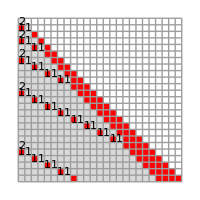
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

evol len: 264

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2}}

Position of first untrustworthy node: {134,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264}

distances (uncut): {0,1,2,3,2,4,5,4,3,3,6,7,6,5,5,4,4,4,4,8,9,8,7,7,6,6,6,6,5,5,5,5,5,5,5,5,10,11,10,9,9,8,8,8,8,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,12,13,12,11,11,10,10,10,10,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,14,15,14,13,13,12,12,12,12,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,16}

last distance we'll trust: 7

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2}}

Position of first untrustworthy node: {134,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264}

distances (uncut): {0,1,2,3,2,4,5,4,3,3,6,7,6,5,5,4,4,4,4,8,9,8,7,7,6,6,6,6,5,5,5,5,5,5,5,5,10,11,10,9,9,8,8,8,8,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,12,13,12,11,11,10,10,10,10,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,14,15,14,13,13,12,12,12,12,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,16}

last distance we'll trust: 7

{{exp,18}}

exp

{exp,{1,0,4,2},3
3
2,3 | 6 | 11 | 20 | 37 | 70 | 135 | 263
3 | 5 | 9 | 17 | 33 | 65 | 128 | 
2 | 4 | 8 | 16 | 32 | 63 |  | }
{exp,{1,0,6,2},1
2
1,1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 |  | }
{exp,{1,0,4,2},2
3
2,2 | 5 | 10 | 19 | 36 | 69 | 134
3 | 5 | 9 | 17 | 33 | 65 | 
2 | 4 | 8 | 16 | 32 |  | }
{exp,{2,0,4,2},1 | 2
1 | 2
1 | 1,1 | 2 | 4 | 7 | 13 | 24 | 46 | 89
1 | 2 | 3 | 6 | 11 | 22 | 43 | 
1 | 1 | 3 | 5 | 11 | 21 |  | }

exp

```mathematica
sssE=SSS[{"BA"->"AAB","A"->"BA"},"A",264,SSSMax->25,SSSSize->{200,200},NetSize->{400,300}, VertexLabels->None];
GuessDimension[sssE]//Column
sssE["Verdict"]
```

If the sessie grows exponentially, growth positions are probably frequent and unimportant.  Only cross-checking with the rule used, done by the included MergeIntervalsByRulesUsed, permits limiting consideration to significant positions.

```mathematica
Length[sssE["Evolution"]]
```

265

CheckDimension identifies the network as exponential soon as the sequence of ratios appears.  FixedPointList would continue until lines have zero length:

```mathematica
FixedPointList[Differences,MaxStateLengthPositions[sssE]]//Column
```

{3,6,11,20,37,70,135,263}
{3,5,9,17,33,65,128}
{2,4,8,16,32,63}
{2,4,8,16,31}
{2,4,8,15}
{2,4,7}
{2,3}
{1}
{}
{}

Interestingly, here the exponential behavior was only found in the DistanceTally data when running averages of pairs of integers were summed, the raw data is harder to recognize:

```mathematica
FixedPointList[Differences,DistanceTally[sssE]]//Column
```

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2}}

Position of first untrustworthy node: {134,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264}

distances (uncut): {0,1,2,3,2,4,5,4,3,3,6,7,6,5,5,4,4,4,4,8,9,8,7,7,6,6,6,6,5,5,5,5,5,5,5,5,10,11,10,9,9,8,8,8,8,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,12,13,12,11,11,10,10,10,10,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,14,15,14,13,13,12,12,12,12,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,16}

last distance we'll trust: 7

{1,2,4,7,13,24,46,89}
{1,2,3,6,11,22,43}
{1,1,3,5,11,21}
{0,2,2,6,10}
{2,0,4,4}
{-2,4,0}
{6,-4}
{-10}
{}
{}

```mathematica
MovingAverage[#,2]& /@ FixedPointList[Differences,DistanceTally[sssE]][[;;-4]]//Column
```

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2}}

Position of first untrustworthy node: {134,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264}

distances (uncut): {0,1,2,3,2,4,5,4,3,3,6,7,6,5,5,4,4,4,4,8,9,8,7,7,6,6,6,6,5,5,5,5,5,5,5,5,10,11,10,9,9,8,8,8,8,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,12,13,12,11,11,10,10,10,10,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,14,15,14,13,13,12,12,12,12,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,16}

last distance we'll trust: 7

{3/2,3,11/2,10,37/2,35,135/2}
{3/2,5/2,9/2,17/2,33/2,65/2}
{1,2,4,8,16}
{1,2,4,8}
{1,2,4}
{1,2}
{1}

### Testing

Still finding some bugs!

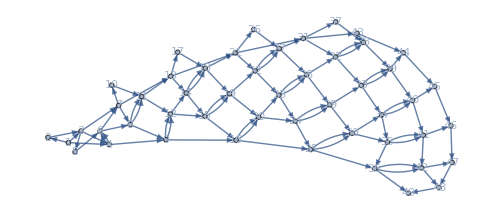
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssTemp=SSS[{"AAB"->"AA","AA"->"ABA","B"->"A"},"AA",300,SSSMax->20,NetMax->49,SSSSize->100,NetSize->500];
```

```mathematica
$debug=False;
CheckDimension@MaxStateLengthPositions[sssTemp]
```

{2D,{1,0,13,2},5
5
2,5 | 10 | 17 | 26 | 37 | 50 | 65 | 82 | 101 | 122 | 145 | 170 | 197 | 226 | 257
5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@LeastUsedRulePositions[sssTemp]
```

{2D,{1,0,14,2},5
5
2,5 | 10 | 17 | 26 | 37 | 50 | 65 | 82 | 101 | 122 | 145 | 170 | 197 | 226 | 257 | 290
5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@DistanceLastPositions[sssTemp]
```

{2D,{1,0,14,2},4
5
2,4 | 9 | 16 | 25 | 36 | 49 | 64 | 81 | 100 | 121 | 144 | 169 | 196 | 225 | 256 | 289
5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@DistanceTally[sssTemp]
```

{2D,{4,0,12,3/2},1 | 4 | 8 | 13
3 | 4 | 5 | 7
1 | 1 | 2 | 2,1 | 4 | 8 | 13 | 20 | 29 | 39 | 50 | 63 | 78 | 94 | 111 | 130 | 151 | 173 | 196 | 221
3 | 4 | 5 | 7 | 9 | 10 | 11 | 13 | 15 | 16 | 17 | 19 | 21 | 22 | 23 | 25 | 
1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 |  | }

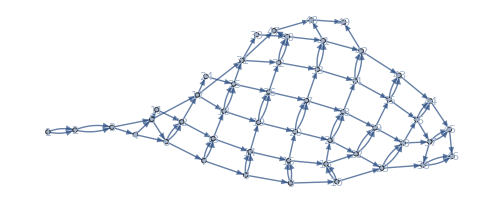
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssTemp1=SSS[{"AAB"->"AA","AA"->"ABA","B"->"A"},"AABBBABAAAA",300,SSSMax->20,NetMax->49,SSSSize->100,NetSize->500];
```

```mathematica
CheckDimension@MaxStateLengthPositions[sssTemp1]
```

{2D,{1,0,10,2},11
13
2,11 | 24 | 39 | 56 | 75 | 96 | 119 | 144 | 171 | 200 | 231 | 264
13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@LeastUsedRulePositions[sssTemp1]
```

{2D,{1,0,11,2},11
13
2,11 | 24 | 39 | 56 | 75 | 96 | 119 | 144 | 171 | 200 | 231 | 264 | 299
13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 35 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@DistanceLastPositions[sssTemp1]
```

{2D,{1,0,11,2},5
12
2,5 | 17 | 31 | 47 | 65 | 85 | 107 | 131 | 157 | 185 | 215 | 247 | 281
12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@DistanceTally[sssTemp1]
```

{2D,{7,1,5,12/7},2 | 3 | 5 | 8 | 13 | 20 | 29
1 | 2 | 3 | 5 | 7 | 9 | 11
1 | 1 | 2 | 2 | 2 | 2 | 2,1 | 2 | 3 | 5 | 8 | 13 | 20 | 29 | 40 | 53 | 67 | 82 | 99 | 118 | 138 | 159
1 | 1 | 2 | 3 | 5 | 7 | 9 | 11 | 13 | 14 | 15 | 17 | 19 | 20 | 21 | 
0 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 |  | }

```mathematica
sssTemp1=SSSEvolve[sssTemp1,300];
```

```mathematica
CheckDimension@DistanceTally[sssTemp1]
```

{failed,1 | 2 | 3 | 5 | 8 | 13 | 20 | 29 | 40 | 53 | 67 | 82 | 99 | 118 | 138 | 159 | 182 | 207 | 233 | 260 | 289 | 320 | 352
1 | 1 | 2 | 3 | 5 | 7 | 9 | 11 | 13 | 14 | 15 | 17 | 19 | 20 | 21 | 23 | 25 | 26 | 27 | 29 | 31 | 32 | 
0 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 |  | 
1 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | -1 |  |  | 
-1 | 1 | -1 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 |  |  |  | 
2 | -2 | 1 | 0 | 0 | -1 | 2 | 0 | -2 | 0 | 2 | 0 | -2 | 0 | 2 | 0 | -2 | 0 |  |  |  |  | 
-4 | 3 | -1 | 0 | -1 | 3 | -2 | -2 | 2 | 2 | -2 | -2 | 2 | 2 | -2 | -2 | 2 |  |  |  |  |  | 
7 | -4 | 1 | -1 | 4 | -5 | 0 | 4 | 0 | -4 | 0 | 4 | 0 | -4 | 0 | 4 |  |  |  |  |  |  | 
-11 | 5 | -2 | 5 | -9 | 5 | 4 | -4 | -4 | 4 | 4 | -4 | -4 | 4 | 4 |  |  |  |  |  |  |  | 
16 | -7 | 7 | -14 | 14 | -1 | -8 | 0 | 8 | 0 | -8 | 0 | 8 | 0 |  |  |  |  |  |  |  |  | 
-23 | 14 | -21 | 28 | -15 | -7 | 8 | 8 | -8 | -8 | 8 | 8 | -8 |  |  |  |  |  |  |  |  |  | 
37 | -35 | 49 | -43 | 8 | 15 | 0 | -16 | 0 | 16 | 0 | -16 |  |  |  |  |  |  |  |  |  |  | 
-72 | 84 | -92 | 51 | 7 | -15 | -16 | 16 | 16 | -16 | -16 |  |  |  |  |  |  |  |  |  |  |  | 
156 | -176 | 143 | -44 | -22 | -1 | 32 | 0 | -32 | 0 |  |  |  |  |  |  |  |  |  |  |  |  | 
-332 | 319 | -187 | 22 | 21 | 33 | -32 | -32 | 32 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
651 | -506 | 209 | -1 | 12 | -65 | 0 | 64 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1157 | 715 | -210 | 13 | -77 | 65 | 64 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1872 | -925 | 223 | -90 | 142 | -1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-2797 | 1148 | -313 | 232 | -143 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3945 | -1461 | 545 | -375 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | }

```mathematica
sssTemp1=SSSEvolve[sssTemp1,300];
```

```mathematica
CheckDimension@DistanceTally[sssTemp1]
```

{failed,1 | 2 | 3 | 5 | 8 | 13 | 20 | 29 | 40 | 53 | 67 | 82 | 99 | 118 | 138 | 159 | 182 | 207 | 233 | 260 | 289 | 320 | 352 | 385 | 420 | 457 | 495 | 534
1 | 1 | 2 | 3 | 5 | 7 | 9 | 11 | 13 | 14 | 15 | 17 | 19 | 20 | 21 | 23 | 25 | 26 | 27 | 29 | 31 | 32 | 33 | 35 | 37 | 38 | 39 | 
0 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 |  | 
1 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | -1 | 0 |  |  | 
-1 | 1 | -1 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 |  |  |  | 
2 | -2 | 1 | 0 | 0 | -1 | 2 | 0 | -2 | 0 | 2 | 0 | -2 | 0 | 2 | 0 | -2 | 0 | 2 | 0 | -2 | 0 | 2 |  |  |  |  | 
-4 | 3 | -1 | 0 | -1 | 3 | -2 | -2 | 2 | 2 | -2 | -2 | 2 | 2 | -2 | -2 | 2 | 2 | -2 | -2 | 2 | 2 |  |  |  |  |  | 
7 | -4 | 1 | -1 | 4 | -5 | 0 | 4 | 0 | -4 | 0 | 4 | 0 | -4 | 0 | 4 | 0 | -4 | 0 | 4 | 0 |  |  |  |  |  |  | 
-11 | 5 | -2 | 5 | -9 | 5 | 4 | -4 | -4 | 4 | 4 | -4 | -4 | 4 | 4 | -4 | -4 | 4 | 4 | -4 |  |  |  |  |  |  |  | 
16 | -7 | 7 | -14 | 14 | -1 | -8 | 0 | 8 | 0 | -8 | 0 | 8 | 0 | -8 | 0 | 8 | 0 | -8 |  |  |  |  |  |  |  |  | 
-23 | 14 | -21 | 28 | -15 | -7 | 8 | 8 | -8 | -8 | 8 | 8 | -8 | -8 | 8 | 8 | -8 | -8 |  |  |  |  |  |  |  |  |  | 
37 | -35 | 49 | -43 | 8 | 15 | 0 | -16 | 0 | 16 | 0 | -16 | 0 | 16 | 0 | -16 | 0 |  |  |  |  |  |  |  |  |  |  | 
-72 | 84 | -92 | 51 | 7 | -15 | -16 | 16 | 16 | -16 | -16 | 16 | 16 | -16 | -16 | 16 |  |  |  |  |  |  |  |  |  |  |  | 
156 | -176 | 143 | -44 | -22 | -1 | 32 | 0 | -32 | 0 | 32 | 0 | -32 | 0 | 32 |  |  |  |  |  |  |  |  |  |  |  |  | 
-332 | 319 | -187 | 22 | 21 | 33 | -32 | -32 | 32 | 32 | -32 | -32 | 32 | 32 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
651 | -506 | 209 | -1 | 12 | -65 | 0 | 64 | 0 | -64 | 0 | 64 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1157 | 715 | -210 | 13 | -77 | 65 | 64 | -64 | -64 | 64 | 64 | -64 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1872 | -925 | 223 | -90 | 142 | -1 | -128 | 0 | 128 | 0 | -128 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-2797 | 1148 | -313 | 232 | -143 | -127 | 128 | 128 | -128 | -128 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3945 | -1461 | 545 | -375 | 16 | 255 | 0 | -256 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-5406 | 2006 | -920 | 391 | 239 | -255 | -256 | 256 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7412 | -2926 | 1311 | -152 | -494 | -1 | 512 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-10338 | 4237 | -1463 | -342 | 493 | 513 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
14575 | -5700 | 1121 | 835 | 20 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-20275 | 6821 | -286 | -815 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | }

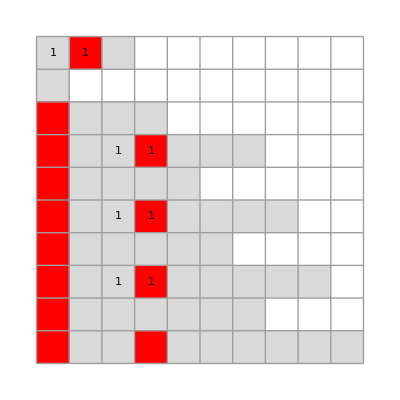
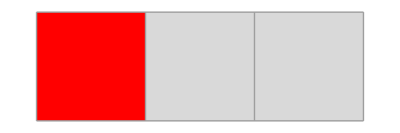
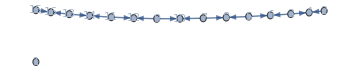
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
Clear[sssT];
sssT=SSS[15900,52,SSSSize->Tiny,NetSize->Medium,SSSMax->10,NetMax->16];
```

```mathematica
CheckDimension@MaxStateLengthPositions[sssT]
sssT["RulesUsed"]
CheckDimension@LeastUsedRulePositions[sssT]
```

{1D,{1,0,23,2},4
2,4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

{1,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}

{1D,{1,1,24,2},4
2,1 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52
3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@DistanceTally[sssT]
```

{1D,{1,0,49,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
sssT["Net"]
```

{3→4,2→4,5→6,3→6,7→8,5→8,9→10,7→10,11→12,9→12,13→14,11→14,15→16,13→16,17→18,15→18,19→20,17→20,21→22,19→22,23→24,21→24,25→26,23→26,27→28,25→28,29→30,27→30,31→32,29→32,33→34,31→34,35→36,33→36,37→38,35→38,39→40,37→40,41→42,39→42,43→44,41→44,45→46,43→46,47→48,45→48,49→50,47→50,51→52,49→52}

```mathematica
Keys[sssT]
```

{Net,OutDegreePotential,OutDegreeRemaining,OutDegreeActual,InDegree,ConnectionList,Verdict,RulesUsed,CellsDeleted,Distance,MaxColor,TagIndex,TEvolution,Evolution,RuleSet,TRuleSet,RuleSetWeight,RuleSetLength}

```mathematica
sssT["Distance"]
```

{0,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

```mathematica
ReliableDistances[sssT]
```

{2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

```mathematica
$debug=True;
ReliableDistances[sssT]
```

smallest node in net: 2

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2,0}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2},{0},{}}

Position of first untrustworthy node: {}

distances (uncut): {2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

last distance we'll trust: ∞

{2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

```mathematica
ReliableDistances[sssT]
```

smallest node in net: 2

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2,0}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2},{0},{}}

Position of first untrustworthy node: {}

distances (uncut): {2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

last distance we'll trust: ∞

{2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

```mathematica
sssT["Net"]
```

{3→4,2→4,5→6,3→6,7→8,5→8,9→10,7→10,11→12,9→12,13→14,11→14,15→16,13→16,17→18,15→18,19→20,17→20,21→22,19→22,23→24,21→24,25→26,23→26,27→28,25→28,29→30,27→30,31→32,29→32,33→34,31→34,35→36,33→36,37→38,35→38,39→40,37→40,41→42,39→42,43→44,41→44,45→46,43→46,47→48,45→48,49→50,47→50,51→52,49→52}

```mathematica
$debug=True;
ReliableDistances[sssT]
```

smallest node in net: 2

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2,0}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2},{0},{}}

Position of first untrustworthy node: {}

distances (uncut): {2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

last distance we'll trust: ∞

{2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

```mathematica
$debug=True;
GuessDimension[sssT]
```

evol len: 52

smallest node in net: 2

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2,0}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2},{0},{}}

Position of first untrustworthy node: {}

distances (uncut): {2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

last distance we'll trust: ∞

Part::take: Cannot take positions 51 through 49 in {1,2,2,1,2,1,2,1,2,1,«42»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted